### Basis:

```mathematica
SpcmNETAssembly=LoadNETAssembly["SpcmDrv64.NET.dll","D:\\Documents\\Spectrum GmbH\\Examples\\.NET"];
```

```mathematica
NETTypeInfo[SpcmNETAssembly]
```

Assembly: SpcmDrv64.NET
Full Name: SpcmDrv64.NET, Version=0.0.0.0, Culture=neutral, PublicKeyToken=null
Location: D:\Documents\Spectrum GmbH\Examples\.NET\SpcmDrv64.NET.dll

● Classes
class Spcm.CardType
class Spcm.Drv
class Spcm.Error
class Spcm.Regs

```mathematica
SpcmDrv=LoadNETType["Spcm.Drv"];
```

```mathematica
NETTypeInfo@SpcmDrv
```

● Type
class Spcm.Drv
Inheritance:
      System.Object
         Spcm.Drv
Interfaces Implemented: None
Assembly-Qualified Name: Spcm.Drv, SpcmDrv64.NET, Version=0.0.0.0, Culture=neutral, PublicKeyToken=null
Assembly Location: D:\Documents\Spectrum GmbH\Examples\.NET\SpcmDrv64.NET.dll

● Constructors
Drv()

● Fields
const int SPCM_BUF_ABA
const int SPCM_BUF_DATA
const int SPCM_BUF_TIMESTAMP
const int SPCM_DIR_CARDTOPC
const int SPCM_DIR_PCTOCARD

● Methods
virtual bool Equals(object obj)
static bool Equals(object objA, object objB)
virtual int GetHashCode()
Type GetType()
static bool ReferenceEquals(object objA, object objB)
static unsigned spcm_dwDefTransfer_i64(IntPtr hDevice, unsigned dwBufType, unsigned dwDirection, unsigned dwNotifySize, IntPtr pBuffer, unsigned long qwBrdOffs, unsigned long qwTransferLen)
static unsigned spcm_dwGetContBuf_i64(IntPtr hDevice, unsigned dwBufType, out IntPtr pBuffer, out unsigned long qwContBufLen)
static unsigned spcm_dwGetErrorInfo_i32(IntPtr hDevice, out unsigned dwErrorReg, out int lErrorValue, System.Text.StringBuilder sErrorText)
static unsigned spcm_dwGetParam_i32(IntPtr hDevice, int lRegister, out int lValue)
static unsigned spcm_dwGetParam_i64(IntPtr hDevice, int lRegister, out long llValue)
static unsigned spcm_dwGetParam_i64m(IntPtr hDevice, int lRegister, out int lValue, out unsigned dwValue)
static unsigned spcm_dwSetParam_i32(IntPtr hDevice, int lRegister, int lValue)
static unsigned spcm_dwSetParam_i64(IntPtr hDevice, int lRegister, long llValue)
static unsigned spcm_dwSetParam_i64m(IntPtr hDevice, int lRegister, int lValueHigh, unsigned dwValueLow)
static IntPtr spcm_hOpen(string szDeviceName)
static void spcm_vClose(IntPtr hDevice)
virtual string ToString()

```mathematica
SpcmDrvObj=NETNew[SpcmDrv];
```

```mathematica
SpcmDev=SpcmDrvObj@spcmUhOpen["TCPIP::192.168.32.36::INSTR"](*connect the awg*)
```

«NETObject[System.IntPtr]»

```mathematica
SpcmDrvObj@spcmUdwGetParamUi64[SpcmDev,2000,$awgCardType](*get card type*)
```

0

```mathematica
SpcmDrvObj@spcmUdwGetParamUi64[SpcmDev,2030,$awgSerialNumber](*get serial number*)
```

0

```mathematica
$awgCardType
```

484913

```mathematica
$awgSerialNumber
```

11558

```mathematica
(*reset the board*)
SpcmDrvObj@spcmUdwSetParamUi32[SpcmDev,100,1];
```

```mathematica
MHz=1000000;GHz=1000000000;
(*set the external clock and sampling rate*)
SpcmDrvObj@spcmUdwSetParamUi32[SpcmDev,20200,32](*enable external reference*);
SpcmDrvObj@spcmUdwSetParamUi32[SpcmDev,20140,10MHz](*external reference clock freq*);
SpcmDrvObj@spcmUdwSetParamUi64[SpcmDev,20000,1GHz](*set the sampling rate*);

(*set the trigger*)
SpcmDrvObj@spcmUdwSetParamUi32[SpcmDev,40410,2](*add the external main trigger to "Or mask"*);
SpcmDrvObj@spcmUdwSetParamUi32[SpcmDev,40510,2](*trigger detection for negative edges*);
SpcmDrvObj@spcmUdwSetParamUi32[SpcmDev,40810,0](*trigger delay is set to zero*);
SpcmDrvObj@spcmUdwSetParamUi32[SpcmDev,40110,0](*trigger impedance is set to high*);
SpcmDrvObj@spcmUdwSetParamUi32[SpcmDev,40120,0](*dc coupling*);

(*set the output channel*)
SpcmDrvObj@spcmUdwSetParamUi32[SpcmDev,11000,1](*activate channel 0*);
SpcmDrvObj@spcmUdwSetParamUi32[SpcmDev,30091,1](*enable the output of channel 0*);
SpcmDrvObj@spcmUdwSetParamUi32[SpcmDev,30010,200](*max amplitude is 200 mV with 50Ω load*);
SpcmDrvObj@spcmUdwSetParamUi32[SpcmDev,30080,0](* no filter is used for channel 0*);
SpcmDrvObj@spcmUdwSetParamUi32[SpcmDev,206020,16](*the output is zero after replay for channel 0*);
```

```mathematica
SpcmDrvObj@spcmUdwGetParamUi64[SpcmDev,9501,a]
a
```

9

0

```mathematica
SpectrumDwGetErrorInfo[SpcmDev]
```

open: card is already in use by another application

### Function:

```mathematica
ClearAll[SpectrumDwGetErrorInfo];
SpectrumDwGetErrorInfo[hDevice_]:=Module[{szErrorTextBuffer=NETNew["System.Text.StringBuilder",100],a,b},SpcmDrvObj@spcmUdwGetErrorInfoUi32[hDevice,a,b,szErrorTextBuffer];
FromCharacterCode@Table[szErrorTextBuffer@Chars[i],{i,0,szErrorTextBuffer@Length-1}]
];

ClearAll[LoadSingleReplayModeSamples];(*参考官方的csharp例子*)
LoadSingleReplayModeSamples[sampleList:{{___Integer}..},hDevice_]:=Module[{lMemsize=32Ceiling@(Max[Length/@sampleList]/32),sample,lBytesPerSample,qwTransferLen,hBufferHandle,pBuffer,errorCode},
SpcmDrvObj@spcmUdwSetParamUi32[hDevice,100,64](*stop current running*);
SpcmDrvObj@spcmUdwSetParamUi32[hDevice,9500,32768](*single replay mode*);
sample=Flatten[Table[PadRight[Mod[sample,65536,-32768],lMemsize],{sample,sampleList}]ᵀ];
SpcmDrvObj@spcmUdwGetParamUi32[SpcmDev,1120,lBytesPerSample];
qwTransferLen=lBytesPerSample*Length@sample;
If[qwTransferLen==0,Return[]];
(* SPC_MEMSIZE *)
SpcmDrvObj@spcmUdwSetParamUi64[hDevice,10000,lMemsize](*set the memory size*);
SpcmDrvObj@spcmUdwSetParamUi32[hDevice,10020,1](*set the loop number*);
hBufferHandle=NETNew["System.Runtime.InteropServices.GCHandle"]@Alloc[MakeNETObject[sample,"System.Int16[]"],NETNew["System.Runtime.InteropServices.GCHandleType"]@Pinned];
pBuffer=hBufferHandle@AddrOfPinnedObject[];
errorCode=SpcmDrvObj@spcmUdwDefTransferUi64[hDevice,1000,0,0,pBuffer,0,qwTransferLen](*transfer the data*);
(* SPC_M2CMD *)
SpcmDrvObj@spcmUdwSetParamUi64[hDevice,100,196608];
SpcmDrvObj@spcmUdwSetParamUi64[hDevice,100,12](*参考awg手册84页的example*);
errorCode
];

ClearAll[GenerateSamples];
GenerateSamples[signal:{{Except@_List,_?NumberQ,_?NumberQ}..},{rate_?NumberQ,trigger_?NumberQ},{resolution_Integer,default_Integer}]:=Module[{t1=⌈rate trigger⌉,sample={},sig,fig={},t0,t},
Do[t0=⌈rate sig⟦2⟧⌉;If[t0>t1,sample=Join[sample,Table[default,t0-t1]],t0=t1];
t1=⌈rate sig⟦3⟧⌉;If[t1>t0,AppendTo[fig,Plot[default+resolution(First@sig/."t"->t/rate),{t,t0,t1}]];sig=Compile[{{t,_Integer}},Evaluate[default+Round[resolution(First@sig/."t"->t/rate)]]];sample=Join[sample,Table[sig@t,{t,t0,t1-1}]],t1=t0],{sig,signal}];
Print[Show@@Join[fig,{ListPlot[Table[{i-1,sample[[i]]},{i,Length@sample}],PlotStyle->Red]}]];
sample];
```

### Test:

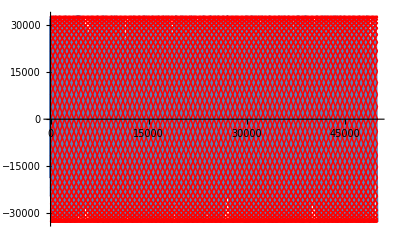

```mathematica
sample=GenerateSamples[{{Cos[2π*173.05"t"],0,50}},{1000,0},{32767,0}];
```

```mathematica
LoadSingleReplayModeSamples[{sample},SpcmDev]
```

0

```mathematica
SequenceFile["Sequence/Raman.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[5],"AWG"[1],"Raman"[1],"Detection"[300,1,1],"Zero"[1]}]
```

D:\Data\Sequence\Raman.seq

```mathematica
SpcmDrvObj@spcmUvClose[SpcmDev](*disconnect the awg*)
ReleaseNETObject@SpcmDev
```